## Getting the Data From a Formated File

## Getting the List From the file generated by the c++ project

```mathematica
s=ToExpression[Import[NotebookDirectory[]<>"/Unified Cruncher/formated.txt"]];
```

Import::nffil: File not found during Import.

$Failed

change Make path sure the you

```mathematica
$RootDirectory
```

## s is now a list in this formate {“country”,{feild1,feild2,year},{feild1,feild2,year} ... Each feild in a backets is a new data point from those feilds

## This function will get the data that is only for the country specified

```mathematica
getCount[name_]:=l[[Position[l[[All,1]],name][[1]]]][[1]]
```

## This Fuction will return the raw data points: {{feild1,feild2}1,{feild1,feild2}2...

```mathematica
getPure[country_]:=getCount[country][[2;;]][[All,1;;2]]
```

## These Fuctions will Create non linear Regressions one with a log base the other with a exponent base. Remeber the first feild is the x axis (domain) and the second feild is the y

```mathematica
nlmLog[country_]:=NonlinearModelFit[getPure[country],c*Log[a+b*x],{a,b,c},x]
```

```mathematica
nlmE[country_]:=NonlinearModelFit[getPure[country],a*x^2+b*x+c,{a,b,c},x]
```

```mathematica
Import[NotebookDirectory[]<>"/formated.txt"]
```

## Now These Function will Graph the Models with the underlying data points. Again one for each kind of model

```mathematica
SideGraphLog[country_]:=Show[ListPlot[getPure[country]],Plot[nlmLog[country][i],{i,Min[getPure[country][[All,1]]],Max[getPure[country][[All,1]]]}]]
```

```mathematica
SideGraphE[country_]:=
Show[ListPlot[getPure[country]],Plot[nlmE[country][i],{i,Min[getPure[country][[All,1]]],Max[getPure[country][[All,1]]]}]]
```

Testing

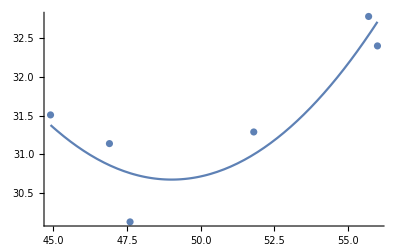

```mathematica
SideGraphE["Germany"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

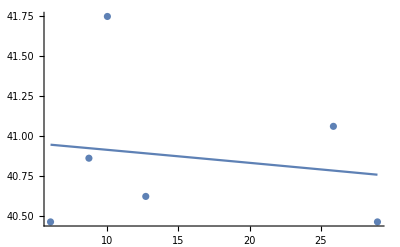

```mathematica
SideGraphLog["United States"]
```

If the model generated does not fit the data this will happen

NonlinearModelFit::nrlnum: The function value {13.1682+19.8213 ⅈ,13.2068+19.8213 ⅈ,12.414+19.8213 ⅈ,12.4033+19.8213 ⅈ,13.564+19.8213 ⅈ,16.7069+19.8213 ⅈ,15.4682+19.8213 ⅈ,16.4842+19.8213 ⅈ} is not a list of real numbers with dimensions {8} at {a,b,c} = {856.679,-59.6787,6.30931}.

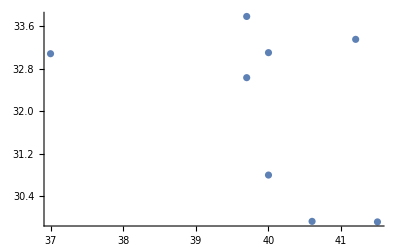

```mathematica
SideGraphLog["France"]
```